```mathematica
s=NDSolve[{x'[t]==-y[t]+x[t],y'[t]==1-x[t]^2,x[0]==1,y[0]==1.5},{x,y},{t,0,2}]
```

{{x→InterpolatingFunction[{{0., 2.}}, <>],y→InterpolatingFunction[{{0., 2.}}, <>]}}

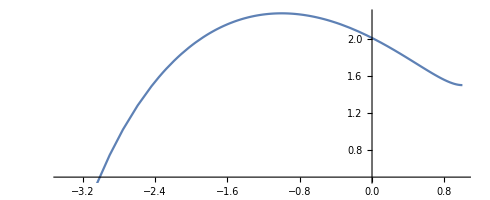

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,2}]
```

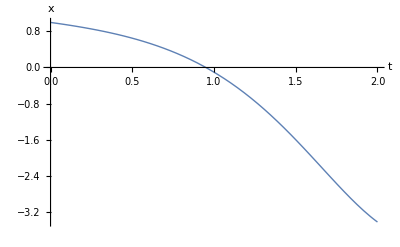

```mathematica
Plot[Evaluate[x[t]/.s],{t,0,2},LabelStyle->Large,PlotStyle->Thick,AxesLabel->{"t","x"}]
```

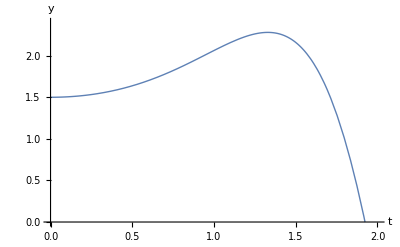

```mathematica
Plot[Evaluate[y[t]/.s],{t,0,2},LabelStyle->Large,PlotStyle->Thick,AxesLabel->{"t","y"},PlotRange->{0,2.4}]
```

```mathematica
sB=NDSolve[{x'[t]==y[t]-x[t],y'[t]==1-x[t]^2,x[0]==1,y[0]==1.5},{x,y},{t,0,2}]
```

{{x→InterpolatingFunction[{{0., 2.}}, <>],y→InterpolatingFunction[{{0., 2.}}, <>]}}

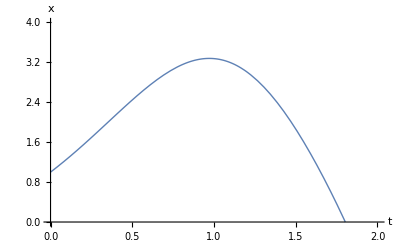

```mathematica
Plot[Evaluate[x[t]/.sB],{t,0,2},LabelStyle->Large,PlotStyle->Thick,AxesLabel->{"t","x"},PlotRange->{0,4}]
```

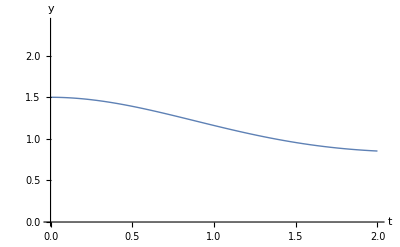

```mathematica
Plot[Evaluate[y[t]/.sB],{t,0,2},LabelStyle->Large,PlotStyle->Thick,AxesLabel->{"t","y"},PlotRange->{0,2.4}]
```

```mathematica
sC=NDSolve[{x'[t]==y[t]+x[t],y'[t]==1-x[t]^2,x[0]==0,y[0]==.5},{x,y},{t,0,2}]
```

{{x→InterpolatingFunction[{{0., 2.}}, <>],y→InterpolatingFunction[{{0., 2.}}, <>]}}

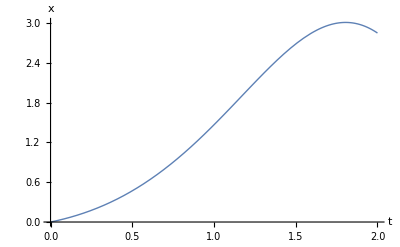

```mathematica
Plot[Evaluate[x[t]/.sC],{t,0,2},LabelStyle->Large,PlotStyle->Thick,AxesLabel->{"t","x"}]
```

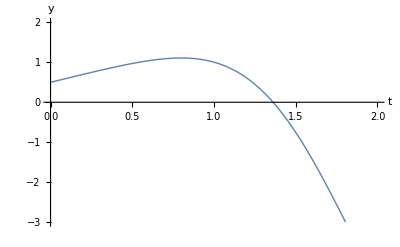

```mathematica
Plot[Evaluate[y[t]/.sC],{t,0,2},LabelStyle->Large,PlotStyle->Thick,AxesLabel->{"t","y"},PlotRange->{-3,2}]
```

```mathematica
sD=NDSolve[{x'[t]==-y[t]-x[t],y'[t]==1-x[t]^2,x[0]==1,y[0]==1.5},{x,y},{t,0,2}]
```

{{x→InterpolatingFunction[{{0., 2.}}, <>],y→InterpolatingFunction[{{0., 2.}}, <>]}}

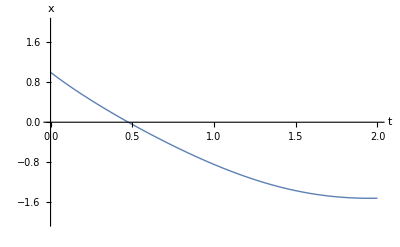

```mathematica
Plot[Evaluate[x[t]/.sD],{t,0,2},LabelStyle->Large,PlotStyle->Thick,AxesLabel->{"t","x"},PlotRange->{-2,2}]
```

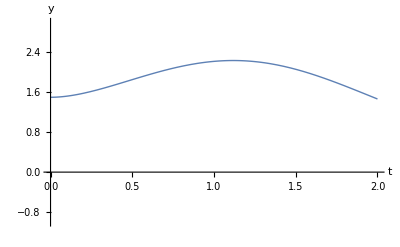

```mathematica
Plot[Evaluate[y[t]/.sD],{t,0,2},LabelStyle->Large,PlotStyle->Thick,AxesLabel->{"t","y"},PlotRange->{-1,3}]
```